```mathematica
DSolve[{y'[x]==Sin[5*x]},y[x],x]
```

{{y[x]→C[1]-1/5 Cos[5 x]}}

```mathematica
DSolve[{x^2*y'[x]==y[x]-y[x]*x},y[x],x]
```

{{y[x]→(ⅇ^(-1/x) C[1])/x}}

```mathematica
DSolve[{x^2*y'[x]==y[x]-y[x]*x,y[1]==1/ⅇ},y[x],x]
```

{{y[x]→ⅇ^(-1/x)/x}}

```mathematica
DSolve[{y''[x]+5y'[x]+2y[x]==0,y[0]==5,y'[0]==10},y[x],x]
```

{{y[x]→-5/34 (-17 ⅇ^((-5/2-(√17)/2) x)+9 √17 ⅇ^((-5/2-(√17)/2) x)-17 ⅇ^((-5/2+(√17)/2) x)-9 √17 ⅇ^((-5/2+(√17)/2) x))}}

```mathematica
DSolve[{y''[x]+5y'[x]+2y[x]==0},y[x],x]
```

{{y[x]→ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
a=NDSolve[{y''[x]+x*y[x]==0,y[0]==1,y[1]==1},y[x],{x,-5,10}]
```

{{y[x]→InterpolatingFunction[{{-5.,10.}},<>][x]}}

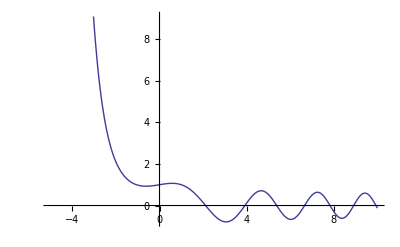

NDSolve::deqn: Equation or list of equations expected instead of 1 in the first argument y[t] + SuperscriptBox[1SuperscriptBox[.

```mathematica
Plot[Evaluate[y[x]/.a],{x,-5,10}]
```

```mathematica
b=NDSolve[{y''[t]+(y'[t]+1)^2*y'[t]+y[t]==0,y[0]=1,y'[0]==0},y[t],{t,0,10}]
```

NDSolve::deqn: Equation or list of equations expected instead of 1 in the first argument y[t] + SuperscriptBox[1SuperscriptBox[.

NDSolve[{y[t]+y'[t] (1+y'[t])^2+y''[t]==0,1,y'[0]==0},y[t],{t,0,10}]